# Crack the MJO Nut

Baoxiang Pan
2017.6.28

## Background

Observed Facts

-Graphics-

NOAA Climate.gov animation, adapted from original images provided by Carl Schreck:

```mathematica
GraphicsGrid[ArrayReshape[Import["/Users/lambda/Desktop/MJO.gif"],{4,2}],
Spacings->{10,-120},
ImageSize->Full]
```

-Graphics-

Green shading: below-average outgoing longwave radiation(wave length from 4 µm to 40 µm) values, indicating more clouds and rainfall.

brown shading: above-average OLR (drier and clearer skies than normal).

purple contour: the location and strength of the Pacific jet at the 200-hPa level (roughly 38,000 feet at that location).

Definition

Organized convection motion at planetary scales and to propagate eastward at an averaged speed of 5 m/s across the equatorial Indian and western/central Pacific oceans, with a local intraseasonal period of 30–90 days.

Connection with extra-tropical weather/climate

Tropical heat sources generate subtropical Rossby wave vorticity anomalies that are partially responsible for the retraction (extension) of the Pacific jet stream exit region and the formation of PNP anomalies

For east Pacific, wet (dry) events are favored during the phase of the oscillation associated with enhanced convection near 150 E (120 E) in the tropical Pacific.

Numerical Representation of MJO (which fundamental characteristics of the MJO should be used to define it)

Current Ability of NWM to capture MJO

Impacts on West Coast United States

### California

The frequency of extreme events are more common when tropical activity associated with the MJO is high, as opposed to periods of quiescent phases of the oscillation. Second, a slight preference for a higher number of events is observed when convective anomalies are located in the Indian Ocean. In this situation, low-level westerly and easterly wind anomalies are observed over the Indian and western Pacific Oceans, respectively. The analysis of the interannual variability in the amplitude of the MJO and the occurrence of extreme events over California indicates no direct and systematic relationships with the number of extreme events.

### Oregon and Washington States

The results indicate that the phase of the MJO has a substantial systematic effect on intraseasonal variability in precipitation in Oregon and Washington in both early winter (October–December) and late winter (January–March). The MJO is also associated with a statistically significant enhancement and modulation of floods in early winter. The phases of the MJO that promote enhanced precipitation in the mean and increased incidence of western Washington floods are substantially different during early winter than during late winter. It is suggested that this result is attributable to the difference in the atmospheric circulation of the North Pacific in early versus late winter.

MJO teleconnections in the northern extratropics.
Accurate predictions of MJO events are not sufficient
for successful subseasonal forecasts. The ability to
predict the impact of MJO events on the global circulation
is crucial.

The S2S database, a key component
of the World Weather Research Programme
(WWRP)/World Climate Research Programme
(WCRP) Subseasonal to Seasonal Prediction Project
science plan, is currently open to the public. It contains
reforecasts and also near-real-time subseasonal
to seasonal forecasts from all the major operational
centers.

desert of predictability

sudden stratospheric warmings

sudden stratospheric warming indices

The importance of the tropics in extra-tropical weather forecasting has been
illustrated by several authors. Early results from Ferranti et al. ( 1990 ) indicated that
better representation of the MJO led to better mid-latitude forecasts in the northern
hemisphere, and the benefi t of the connection of the MJO and NAO in intra- seasonal
forecasting has been demonstrated in Lin et al. ( 2010a ).

This type of I-know-it-when-I-see-it, but ill-defined situation is ripe for some machine learnin

The ensemble forecast is usually evaluated by comparing the average of the individual forecasts for one forecast variable to the observed value of that variable

Statistical diagnostics have led to a common perception that only few global models can reproduce the MJO. Here we demonstrate, using a method of tracking individual MJO events, that this perception is incorrect. Of 27 global model simulations diagnosed, all produced large-scale slowly eastward propagating signals in precipitation, which are taken as manifestations of the MJO. The difference is some model produced them frequently, others infrequently. There is no statistically significant distinction between the strength and propagation speeds of MJO events produced by most of these models. A hypothesis is proposed to interpret our results: A model can produce the MJO only in a particular background state. If the background state of a model can be constantly in a condition that is conducive to its production of the MJO, this model simulates the MJO frequently. If not, this model can still produce the MJO but only infrequently when its seasonal background state occasionally migrates into a condition that is conducive to its production of the MJO. Preliminary results from testing this hypothesis are presented

```mathematica
slat=10;
elat=32;
slon=118;
elon=135;
```

```mathematica
winter=Flatten[Table[{Range[1+i*73,24+i*73],Range[50+i*73,73+i*73]},{i,0,69}]][[1;;-25]];
```

```mathematica
SetDirectory["/Volumes/lambda/Data/Reanalysis/NCEP/Precipitation"];
file=FileNames["*.nc"];
lat=Import[file[[1]],{"Datasets","lat"}][[slat;;elat]];
lon=Import[file[[1]],{"Datasets","lon"}][[slon;;elon]];
```

```mathematica
centers=Table[Block[{p,cp,T=20},
	p=Import[file[[i]],{"Datasets","prate"}];
	p=p[[;;,slat;;elat,slon;;elon]];
	cp=Table[Total[p[[j;;j+T-1,;;,;;]]],{j,1,Length[p]-T+1,T}];
	Map[{lat[[Position[#,Max[#]][[1,1]]]],
		 lon[[Position[#,Max[#]][[1,2]]]],
		 Max[#]}&,cp]],{i,Length[file]}];
```

```mathematica
Color[x_]:=Blend[{Yellow,Blue},
	(x-Min[amplitudes[[1;;500]]])/(Max[amplitudes[[1;;500]]]-Min[amplitudes[[1;;500]]])];
```

```mathematica
lats=Flatten[Table[Map[#[[1]]&,centers[[i]]],{i,Length[file]}]];
lons=Flatten[Table[Map[#[[2]]&,centers[[i]]],{i,Length[file]}]];
amplitudes=Flatten[Table[Map[#[[3]]&,centers[[i]]],{i,Length[file]}]];
```

```mathematica
color=Map[Color,amplitudes];
```

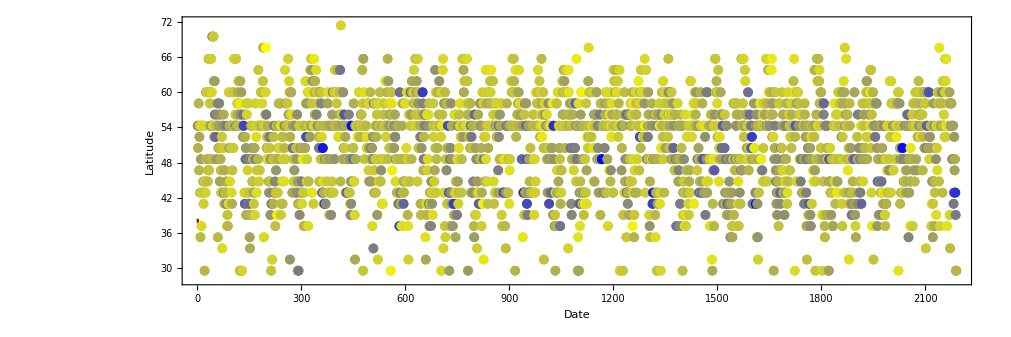

```mathematica
aList = Table[{i,lats[[i]]},{i,Length[lats]}];
colorList = {Black, Red, Blue, Yellow};
bList = {#} & /@ aList;
Show[{ListPlot[bList[[1;;73*30]], 
		 PlotStyle -> color,
		 Frame->True,
		 FrameLabel->{"Date","Latitude"},
		 AspectRatio->1/3,
		 BaseStyle->24,
		 PlotRange->{28,72}],
	   Plot[(65+35)/2.+(65-35)/2*Sin[(x/73)*2Pi-Pi+0.8],{x,1,2},PlotStyle->Dashed]}]
```

```mathematica
𝒟 = SmoothKernelDistribution[Flatten[Table[Map[{#[[1]],#[[3]]}&,centers[[i]]],{i,Length[file]}],1][[winter]]];
TableForm[{Table[ContourPlot[f[𝒟, {x, y}], {x, Min[lats], Max[lats]}, {y, Min[amplitudes], Max[amplitudes]}, 
PlotLabel -> f, PlotRange -> Full], {f, {PDF, CDF}}]}]
```

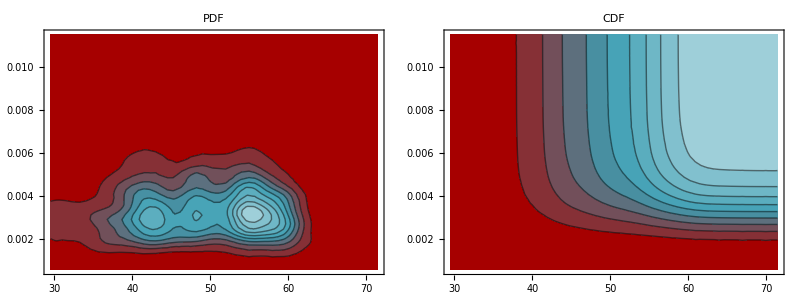

```mathematica
Correlation[lats[[winter]],amplitudes[[winter]]]
```

-0.01915

P = 0.272601>0.05, insignificant

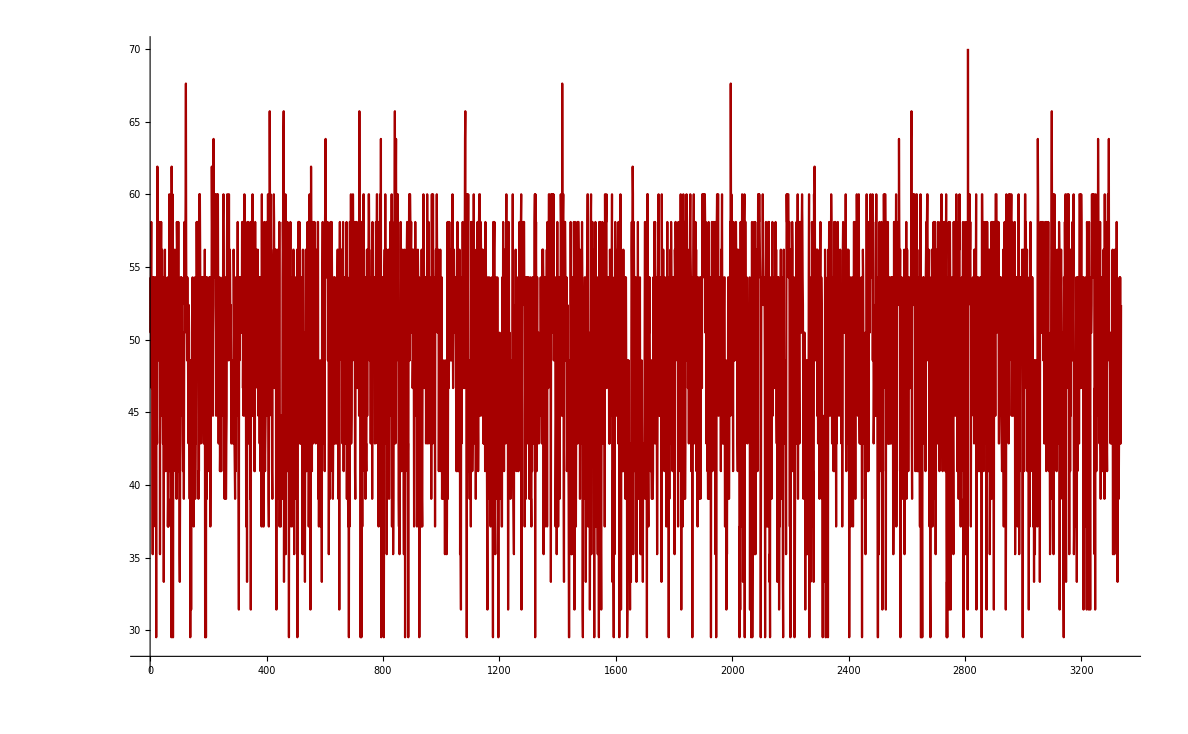

```mathematica
test=Flatten[Table[Map[#[[1]]&,centers[[i]]],{i,Length[file]}]][[winter]];
ListLinePlot[test,PlotRange->{28,70},ImageSize->Large]
```

The intrusion depth in winter is what you want to predict!!!!

```mathematica
TableForm[DFT[amplitudes][[1;;20]]]
```

∞ | 0.00318641 | 0
72.4571 | 0.000458678 | 1.41423
73.5072 | 0.000458477 | -1.82521
36.4892 | 0.000211994 | -0.383106
74.5882 | 0.000173602 | -2.07176
71.4366 | 0.000129684 | 1.2251
24.2679 | 0.000123029 | -2.06897
5072. | 0.000118291 | -1.70457
75.7015 | 0.000106198 | -1.73492
6.62141 | 0.0000873606 | 0.619854
10.501 | 0.0000821188 | 1.20405
24.3846 | 0.0000814378 | 0.707028
281.778 | 0.0000800562 | 2.60278
32.1013 | 0.000078553 | -1.3864
12.401 | 0.0000762574 | -0.199321
6.26947 | 0.0000756494 | -0.898736
80.5079 | 0.0000728456 | -1.85262
2.13199 | 0.0000728454 | -1.16673
5.66704 | 0.0000718382 | -0.678404
8.85166 | 0.0000717805 | 2.64105

```mathematica
DFT[data_, threshold_:0,sort_:1]:= 
 Module[{fs, s1, s = {}, i, mean, af, pf, pos, fr, frpos, fdata, fdatac, n, per,presult},
  n = Length[data];
  fs = Fourier[data];
  s1  = Drop[fs, -Floor[Length[fs]/2]];
  For[i = 2, i <= Length[s1], i++, 
   If[2/Sqrt[n] Abs[fs][[i]] > threshold, 
	 AppendTo[s, i]]];
  mean ={Infinity,Abs[fs[[1]]]/Sqrt[n],0};
  af = 2/Sqrt[n] Abs[fs][[s]];
  pf = Arg[fs][[s]];
  presult=Append[Transpose[{n/(s-1.0), af, pf}],mean];
  If[sort==1,Sort[presult,#1[[2]]>#2[[2]]&],presult]];
DFT::usage="DFT[data]={{T,Amp_max,Phase}...{T,Amp_min,Phase}}\ne.g. DFT[Cos[x]+y]={{∞,y,0},{2π,1,0}}";
```

```mathematica
DFTReconstruct[fp_,n_] := 
  Table[Sum[fp[[j, 2]] Cos[
        2 Pi / fp[[j, 1]] *t - fp[[j, 3]]], {j, 1, 
       Length[fp]}], {t, 0, n-1}];
DFTReconstruct::usage="DFTReconstruct[fp,n]=Reconstructed data(of length n) with frequencies listed in fp";
```

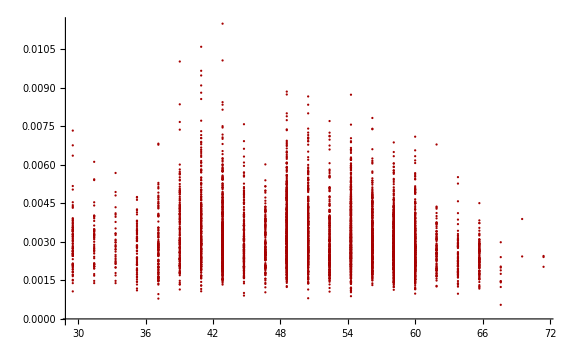

```mathematica
test=Flatten[Table[Map[{#[[1]],#[[3]]}&,centers[[i]]],{i,Length[file]}],1];
ListPlot[test,PlotRange->Full,ImageSize->Large]
```

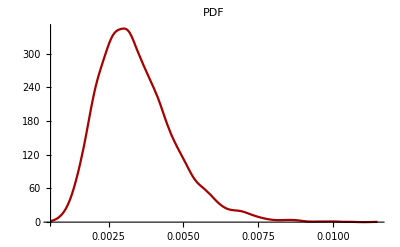
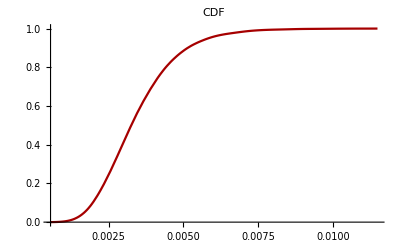

```mathematica
test=Flatten[Table[Map[#[[3]]&,centers[[i]]],{i,Length[file]}],1][[winter]];
𝒟 = SmoothKernelDistribution[test];
Table[Plot[f[𝒟, x], {x, Min[test], Max[test]}, PlotLabel -> f,PlotRange->Full], {f, {PDF, CDF}}]
```

```mathematica
GeoPlot[data_,bounds_]:=Block[{image},
image=ArrayPlot[data,
                 PlotRange->Full,
                 ColorFunction->Hue,
                 Frame->False,
                 PlotRangePadding->None, (* Important *)
                 PlotLegends->Automatic];
Legended[GeoGraphics[
   {{GeoStyling[{"GeoImage", image[[1]]}, 
     GeoRange -> bounds], 
     GeoBoundsRegion[bounds]},  (* image background stretched within bound area *)
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]}},
   GeoProjection ->"Mercator",
   GeoGridLines -> True, 
   GeoRange -> bounds,
   ImageSize -> Medium], 
image[[2]]]]
```

In practical terms, the observed subtropical and extratropical
anomalies associated with the MJO are synonymous
with significant variability of the amplitude and
location of the midlatitude jet

Numerous researchers have indicated that the
MJO may be accompanied by increased predictability in
the subtropics and extratropics

As rightly identified by Cassou (2008),
however, this increased predictability will not be fully realized
until today’s forecast models can properly simulate
not only tropical MJO dynamics but also the tropical–
extratropical interactions that are integral to the evolution
of the atmosphere on the global scale

At any rate, most coupled ocean–atmosphere models are
unable to produce a realistic MJO to this day, and predictions
of the MJO over multiple cycles remain elusive.
Nevertheless, there is potential skill in MJO forecasts
out to a few weeks through extrapolation from current
conditions.

The purpose of this study is to examine further the
impacts of tropical variability associated with the MJO
on cool-season precipitation in the Pacific Northwest.
In essence, we seek to bridge the gap between the climate
perspective provided by Higgins, Mo, and others
and the event-scale perspective provided in the study of
heavy (and warm) rains over western Washington by
Lackmann and Gyakum (1999).